#### Inputs

```mathematica
targetS=-3+4x+2x^2-x^3;
targetS=Cos[x];
range={-3, 4, 0.1};
```

#### Starting

```mathematica
nestS[symb_,var_:x]:=Expand[symb/.var->symb]
funcS[symb_, var_:x]:=Function[dontusethisvariable, symb/.var->dontusethisvariable]
```

```mathematica
target=funcS[targetS];
```

```mathematica
fixedPoints=Sort[If[Im[#]==0,#,Nothing]&/@(Values[#][[1]]&/@NSolve[{x==targetS, x>=range[[1]], x<=range[[2]]}, x]), Less]
middleFixedPoint=fixedPoints[[Round[Length[fixedPoints]/2]]];
```

{0.739085}

```mathematica
(* First two terms of Maclaurin series to make a linear approximation around x = middleFixedPoint *)
macLaurinApproxTerms={target[middleFixedPoint],funcS[D[targetS,x]][middleFixedPoint]};

(* y = term[[1]]+term[[2]](x - fixedPoint) -> y = (term[[1]] - term[[2]]fixedPoint) + term[[2]]x *)
macLaurinSlopeInterceptApproxTerms={macLaurinApproxTerms[[1]] -macLaurinApproxTerms[[2]]*middleFixedPoint, macLaurinApproxTerms[[2]]};

linearRootApproxS=macLaurinSlopeInterceptApproxTerms[[1]]/(1+√macLaurinSlopeInterceptApproxTerms[[2]])+√macLaurinSlopeInterceptApproxTerms[[2]] x
linearRootApprox=funcS[linearRootApproxS];
```

x √(-Sin[List])+(Cos[List]+List Sin[List])/(1+√(-Sin[List]))

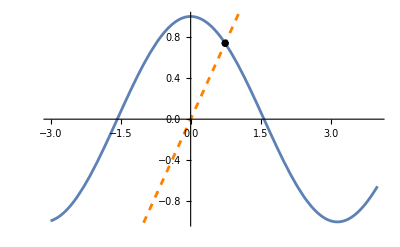

```mathematica
Show[
Plot[target[x], {x, range[[1]], range[[2]]}],
Plot[x, {x, range[[1]], range[[2]]}, PlotStyle->{Orange,Dashed}],
Plot[linearRootApprox[linearRootApprox[linearRootApprox[x]]], {x, range[[1]], range[[2]]}, PlotStyle->Gray],
ListPlot[Transpose[{fixedPoints, fixedPoints}], PlotStyle->Black]]
```

```mathematica
xinit=N[(range[[2]]-range[[1]])/2 + range[[1]]]
w=1;
f[x_]:=target[x];
Min[Abs/@(xinit-fixedPoints)]
```

0.5

0.239085

#### Solving

```mathematica
approxFunc[points_,x_]:=Quiet[Interpolation[points,InterpolationOrder->1][x], InterpolatingFunction::dmval]
asToP[association_]:=Sort[Transpose[{Keys[association], Values[association]}]]
```

```mathematica
findFRL[xi_, wi_]:=findFRL[xi, wi]=Module[{xf=xi, wf=wi, frlf=<||>},
While[range[[1]]<=xf<=range[[2]]&&(Min[Abs/@(xf-fixedPoints)]>=10^-10),
frlf[xf]=wf;
frlf[wf]=f[xf];
wf=f[xf];
xf=wf;]; 
frlf
]
frl1=findFRL[xinit, w]
```

<|0.5→1,1→0.877583,0.877583→0.639012,0.639012→0.802685,0.802685→0.694778,0.694778→0.768196,0.768196→0.719165,0.719165→0.752356,0.752356→0.730081,0.730081→0.74512,0.74512→0.735006,0.735006→0.741827,0.741827→0.737236,0.737236→0.74033,0.74033→0.738246,0.738246→0.73965,0.73965→0.738705,0.738705→0.739341,0.739341→0.738912,0.738912→0.739201,0.739201→0.739007,0.739007→0.739138,0.739138→0.73905,0.73905→0.739109,0.739109→0.739069,0.739069→0.739096,0.739096→0.739078,0.739078→0.73909,0.73909→0.739082,0.739082→0.739087,0.739087→0.739084,0.739084→0.739086,0.739086→0.739084,0.739084→0.739086,0.739086→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085,0.739085→0.739085|>

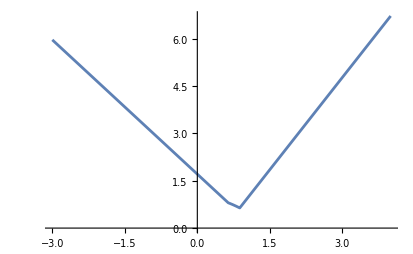

```mathematica
Plot[approxFunc[asToP[frl1],x], {x, range[[1]], range[[2]]}]
```

```mathematica
lenghts={};
points=Flatten[Table[{x, xi, approxFunc[asToP[
(lengths=AppendTo[lengths,Length[#]];#)&@findFRL[xi, 1]],x]}, {x, range[[1]], range[[2]], range[[3]]}, {xi, range[[1]], range[[2]], range[[3]]}], 1];

nestedPoints=Flatten[Table[{x, xi, approxFunc[asToP[findFRL[xi, 1]],approxFunc[asToP[findFRL[xi, 1]],x]]}, {x, range[[1]], range[[2]], range[[3]]}, {xi, range[[1]], range[[2]], range[[3]]}], 1];
```

$Aborted

$Aborted

```mathematica
fewerPoints=Sort@Flatten[Table[Transpose[{ConstantArray[xi, Length[#]],Keys[#],Values[#]}]&@findFRL[xi, 1], {xi, range[[1]], range[[2]], range[[3]]}], 1]
```

{{-3.,-3.,1},{-3.,1,9.},{-2.9,-2.9,1},{-2.9,1,9.},{-2.8,-2.8,1},{-2.8,1,9.},{-2.7,-2.7,1},{-2.7,1,9.},{-2.6,-2.6,1},{-2.6,1,9.},{-2.5,-2.5,1},{-2.5,1,9.},{-2.4,-2.4,1},{-2.4,1,9.},{-2.3,-2.3,1},{-2.3,1,9.},{-2.2,-2.2,1},{-2.2,1,9.},{-2.1,-2.1,1},{-2.1,1,9.},{-2.,-2.,1},{-2.,1,9.},{-1.9,-1.9,1},{-1.9,1,9.},{-1.8,-1.8,1},{-1.8,1,9.},{-1.7,-1.7,1},{-1.7,1,9.},{-1.6,-1.6,1},{-1.6,1,9.},{-1.5,-1.5,1},{-1.5,1,9.},{-1.4,-1.4,1},{-1.4,1,9.},{-1.3,-1.3,1},{-1.3,1,9.},{-1.2,-1.2,1},{-1.2,1,9.},{-1.1,-1.1,1},{-1.1,1,9.},{-1.,-1.,1},{-1.,1,9.},{-0.9,-0.9,1},{-0.9,1,9.},{-0.8,-0.8,1},{-0.8,1,9.},{-0.7,-0.7,1},{-0.7,1,9.},{-0.6,-0.6,1},{-0.6,1,9.},{-0.5,-0.5,1},{-0.5,1,9.},{-0.4,-0.4,1},{-0.4,1,9.},{-0.3,-0.3,1},{-0.3,1,9.},{-0.2,-0.2,1},{-0.2,1,9.},{-0.1,-0.1,1},{-0.1,1,9.},{0.1,0.1,1},{0.1,1,9.},{0.2,0.2,1},{0.2,1,9.},{0.3,0.3,1},{0.3,1,9.},{0.4,0.4,1},{0.4,1,9.},{0.5,2.32831×10^-10,5.42101×10^-20},{0.5,0.0000152588,2.32831×10^-10},{0.5,0.00390625,0.0000152588},{0.5,0.0625,0.00390625},{0.5,0.25,0.0625},{0.5,0.5,1},{0.5,1,0.25},{0.6,0.6,1},{0.6,1,9.},{0.7,0.7,1},{0.7,1,9.},{0.8,0.8,1},{0.8,1,9.},{0.9,0.9,1},{0.9,1,9.},{1.1,1,9.},{1.1,1.1,1},{1.2,1,9.},{1.2,1.2,1},{1.3,1,9.},{1.3,1.3,1},{1.4,1,9.},{1.4,1.4,1},{1.5,1,9.},{1.5,1.5,1},{1.6,1,9.},{1.6,1.6,1},{1.7,1,9.},{1.7,1.7,1},{1.8,1,9.},{1.8,1.8,1},{1.9,1,9.},{1.9,1.9,1},{2.,1,9.},{2.,2.,1},{2.1,1,9.},{2.1,2.1,1},{2.2,1,9.},{2.2,2.2,1},{2.3,1,9.},{2.3,2.3,1},{2.4,1,9.},{2.4,2.4,1},{2.5,1,9.},{2.5,2.5,1},{2.6,1,9.},{2.6,2.6,1},{2.7,1,9.},{2.7,2.7,1},{2.8,1,9.},{2.8,2.8,1},{2.9,1,9.},{2.9,2.9,1},{3.,1,9.},{3.,3.,1},{3.1,1,9.},{3.1,3.1,1},{3.2,1,9.},{3.2,3.2,1},{3.3,1,9.},{3.3,3.3,1},{3.4,1,9.},{3.4,3.4,1},{3.5,1,9.},{3.5,3.5,1},{3.6,1,9.},{3.6,3.6,1},{3.7,1,9.},{3.7,3.7,1},{3.8,1,9.},{3.8,3.8,1},{3.9,1,9.},{3.9,3.9,1},{4.,1,9.},{4.,4.,1}}

```mathematica
plotRange=AbsoluteOptions[ListPointPlot3D[fewerPoints],PlotRange][[1,2]];
Manipulate[ListPointPlot3D[fewerPoints[[;;n]], PlotRange->plotRange], {n, 1,Length[fewerPoints],1}]
```

Part::take: Cannot take positions 1 through 1 in fewerPoints.

Automatic::prng: 
   Value of option PlotRange -> plotRange
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

Part::partd: Part specification 0[[2]] is longer than depth of object.

ListPointPlot3D::ldata: 
   fewerPoints[[1 ;; 1]] is not a valid dataset or list of datasets.

Part::take: Cannot take positions 1 through 1 in fewerPoints.

Automatic::prng: Value of option PlotRange -> plotRange is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

ListPointPlot3D::ldata: fewerPoints⟦1;;1⟧ is not a valid dataset or list of datasets.

```mathematica
ListPlot3D[fewerPoints, AxesLabel->{"x", "xi", "z"}, Mesh->All]
ListPlot3D[nestedPoints, AxesLabel->{"x", "xi", "z"}]
```

-Graphics3D-

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[approxFunc[asToP[
(lengths=AppendTo[lengths,Length[#]];#)&@findFRL[xi, 1]],x], {x, range[[1]], range[[2]], range[[3]]}, {xi, range[[1]], range[[2]], range[[3]]}]
```

Plot3D::pllim: Range specification {x,range⟦1⟧,range⟦2⟧,range⟦3⟧} is not of the form {x, xmin, xmax}.

Plot3D[approxFunc[asToP[((lengths=AppendTo[lengths,Length[#1]];#1)&)[findFRL[xi,1]]],x],{x,range⟦1⟧,range⟦2⟧,range⟦3⟧},{xi,range⟦1⟧,range⟦2⟧,range⟦3⟧}]